# 2D FEA Build

We want to solve the TWO dimensional damped wave equation
	u_tt+c u_t=k Δu
on a domain Ω with Dirichlet conditions u=0 on the boundary ∂Ω

Our spatial Weak Form is for all v∈H_0^1(Ω)

∫_Ω u_tt v dA +c∫_Ω u_t v dA =-k∫_Ω ∇u.∇v dA

We mesh the region with a VERY coarse mesh

We let the mesher pick the order for the vertices and triangles.

We do not need to solve for border vertices since the boundary conditions tell us u|_(∂Ω)=0.

We are going to use our FEA structure and manually build up the matrices for our FEA stuff.

The counting scheme for vertices and elements is no longer obvious.

The mesh is everything: the nodes; the triangles; the numbering scheme; and the connectivity information.

As before could people remind me to take pics of the board as we go.

## Mesh Pic

Computer will draw things in 2D and 3D.  I need to trick the computer into plotting 1D things!

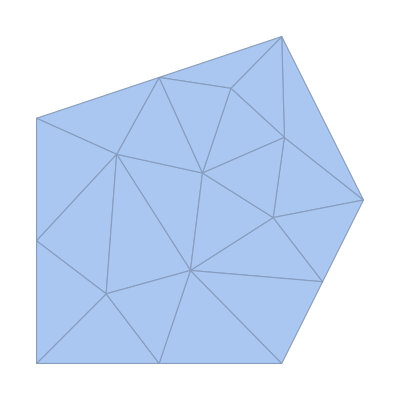

```mathematica
Omega = Polygon[{{0,0},{3,0},{4,2},{3,4},{0,3}}];
TestMesh=DiscretizeRegion[Omega,MaxCellMeasure->0.9]
```

We are going to extract the points from the mesh and we are going to extract the points from the matching boundary mesh.

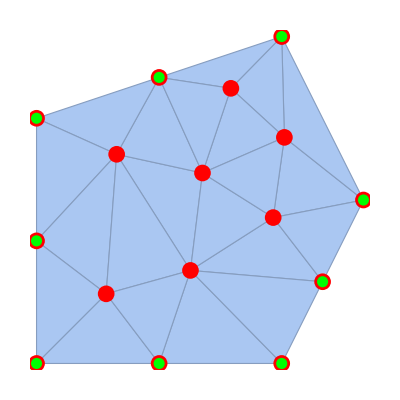

```mathematica
AllPoints= MeshCoordinates[TestMesh];
BoundaryPoints=MeshCoordinates[BoundaryMesh[TestMesh]];
Show[TestMesh,
Graphics[{
{Red, PointSize[0.03],Point[AllPoints]},
{Green,PointSize[0.02],Point[BoundaryPoints]}}]]
```

We need to extract the triangles!  The points are numbered as in AllPoints

```mathematica
TestTriangles = MeshCells[TestMesh,2]
```

{Polygon[{2,12,10}],Polygon[{7,14,3}],Polygon[{12,8,14}],Polygon[{12,11,15}],Polygon[{3,4,7}],Polygon[{7,4,9}],Polygon[{9,11,7}],Polygon[{6,15,11}],Polygon[{4,6,9}],Polygon[{8,12,2}],Polygon[{5,15,6}],Polygon[{6,11,9}],Polygon[{5,13,15}],Polygon[{12,14,11}],Polygon[{15,13,16}],Polygon[{16,1,10}],Polygon[{15,16,12}],Polygon[{3,14,8}],Polygon[{11,14,7}],Polygon[{1,16,13}],Polygon[{10,12,16}]}

Lets check that we know how to do this.

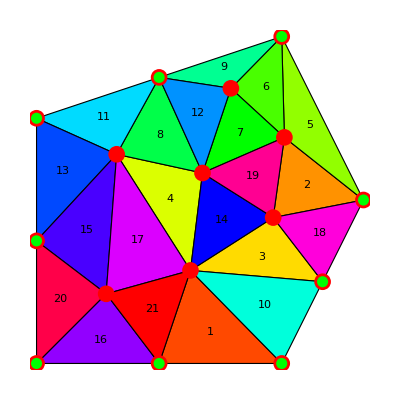

```mathematica
m=Length[TestTriangles];
Graphics[{ EdgeForm[Black],
Table[
{j1,j2,j3}=TestTriangles⟦i,1⟧;
{p1,p2,p3}=AllPoints⟦{j1,j2,j3}⟧;
{{Hue[i/m],Polygon[{p1,p2,p3}]}, Text[i,(p1+p2+p3)/3]},
{i,1,m}],
{Red, PointSize[0.03],Point[AllPoints]},
{Green,PointSize[0.02],Point[BoundaryPoints]}
}]
```

We need to use the triangles and coordinates to build our tent functions.

## Point and Triangle Labels!

Remember we label the tent functions by the label for their peak.  We only need the triangle numbers to know how to build the matrix entries.

```mathematica
BackgroundPic=Graphics[{ EdgeForm[Black],
Table[
{j1,j2,j3}=TestTriangles⟦i,1⟧;
{p1,p2,p3}=AllPoints⟦{j1,j2,j3}⟧;
{Hue[i/m],Polygon[{p1,p2,p3}]},
{i,1,m}],
{Red, PointSize[0.03],Point[AllPoints]},
{Green,PointSize[0.02],Point[BoundaryPoints]}
}];
TabView[{
"Triangles"->Show[
BackgroundPic,
Epilog->Table[
{j1,j2,j3}=TestTriangles⟦i,1⟧;
{p1,p2,p3}=AllPoints⟦{j1,j2,j3}⟧;
Text[i,(p1+p2+p3)/3],
{i,1,m}]],
"Points"-> Show[
BackgroundPic,
Epilog->Table[
p=AllPoints⟦j⟧;
Text[j,p,{-1,-1},Background->White],
{j,1,Length[AllPoints]}]],
"Both"-> Show[
BackgroundPic,
Epilog->{Table[
{j1,j2,j3}=TestTriangles⟦i,1⟧;
{p1,p2,p3}=AllPoints⟦{j1,j2,j3}⟧;
Text[i,(p1+p2+p3)/3],
{i,1,m}],
Table[
p=AllPoints⟦j⟧;
Text[j,p,{-1,-1},Background->White],
{j,1,Length[AllPoints]}]}]
}]
```

123

## Slab Functions

Each triangle has three slab functions associated with it. I need to compute them.  We can do this with some geometry!  What I need the gradient for each bit!    Once we are done the following function should return the triangle as a polygon and the gradient for each of the slab functions!

Here are the three slab functions (look at the clean tidy formulas) on our reference triangle.

```mathematica
Plot3D[{X, Y, 1- (X+  Y)}, {X,0,1},{Y,0,1-X}]
```

-Graphics3D-

There are several ways to think about doing this:  the cleanest solution (and what is done in practice) is to map the simple functions on the reference triangle to the physical triangle.  There are a couple of other solutions that I can see!

The first thing to do is describe what we are looking for! We have three points {x_1,y_1}, {x_2,y_2}, and {x_3,y_3} and we want a linear function that is 1 at {x_1,y_1} and 0 at the other two points.

### Geometric Construction

A geometric construction could go something like this: the gradient g is a constant vector; since the line from {x_2,y_2} to {x_3,y_3} is a zero contour of the function g must be perpendicular to {x_3,y_3}-{x_2,y_2}; since the function goes down from 1 (at {x_1,y_1}) to zero (along the zero contour at the edge opposite {x_1,y_1}) the magnitude of g must equal the reciprocal of the perpendicular distance from {x_1,y_1} to the opposite edge, the last thing we need to do is compute

```mathematica
Clear[PolygonAndSlabFunctionGradients]
PolygonAndSlabFunctionGradients[AllPoints_,TestTriangles_][i_]:= Module[{p1,p2,p3,poly,τ1,τ2,τ3, h1,h2,h3,l1,l2,l3,g1,g2,g3},
{p1,p2,p3}=AllPoints⟦TestTriangles⟦i,1⟧⟧;
poly=Polygon[{p1,p2,p3}];
(* Compute unit tangents of edges *)
{τ1,τ2,τ3}=Map[Normalize,{p2-p3,p3-p1,p1-p2}];
(* Compute height vectors to mid points of edges *)
{h1,h2,h3}={0.5(p2+p3)-p1, 0.5(p3+p1)-p2,0.5(p2+p1)-p3};
(* Project out tangents *)
{h1,h2,h3}={h1-(τ1.h1)τ1, h2-(τ2.h2)τ2, h3-(τ3.h3)τ3};
(* Compute Lengths *)
{l1,l2,l3}=Map[Norm,{h1,h2,h3}];
(* Compute gradients following the argument above formula *)
{g1,g2,g3}={-h1/l1^2,-h2/l2^2,-h3/l3^2};
(* Return pieces to build function *)
{poly, {{p1,p2,p3},{g1,g2,g3}}}
]
```

We should be able to tell we got it correct by plotting the three slab functions.

```mathematica
i=4;
{poly,{{p1,p2,p3},{g1,g2,g3}}}=PolygonAndSlabFunctionGradients[AllPoints,TestTriangles][i];
s1[{x_,y_}]:=If[RegionMember[poly,{x,y}],1+g1.({x,y}-p1),0]
s2[{x_,y_}]:=If[RegionMember[poly,{x,y}],1+g2.({x,y}-p2),0]
s3[{x_,y_}]:=If[RegionMember[poly,{x,y}],1+g3.({x,y}-p3),0]
Plot3D[ {s1[{x,y}],s2[{x,y}],s3[{x,y}]},{x,y}∈ poly]
```

-Graphics3D-

### Algebraic Construction

An algebraic construction could go something like this: each underlying slab linear function is of the form 
	s[{x,y}]=a+b x + c y
and for each of the slabs I have three conditions.  For instance, for s1 we need
	a | + | b x_1 | + | c y_1 | = | 1
a | + | b x_2 | + | c y_2 | = | 0
a | + | b x_3 | + | c y_3 | = | 0 
Three linear equations in three unknowns. So we know what to do. 
	(1 | x_1 | y_1
1 | x_2 | y_2
1 | x_3 | y_3).(a
b
c)=(1
0
0)
Unsurprisingly you get the coefficients for the other slab functions by replacing the RHS with {0,1,0} and {0,0,1}.

```mathematica
Clear[PolygonAndSlabFunctions]
PolygonAndSlabFunctions[AllPoints_,TestTriangles_,{x_Symbol,y_Symbol}][i_]:= Module[{x1,y1,x2,y2,x3,y3,poly, M,InvM},
{{x1,y1},{x2,y2},{x3,y3}}=AllPoints⟦TestTriangles⟦i,1⟧⟧;
poly=Polygon[{{x1,y1},{x2,y2},{x3,y3}}];
(* Build Matrix *)
M = ({{1, x1, y1}, {1, x2, y2}, {1, x3, y3}});
(* Invert to solve block RHS ({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}}) *)
InvM=Inverse[M];
(* Extract Coefficients to build linear functions *)
(* Return pieces to build function *)
{poly, {
InvM⟦1,1⟧+InvM⟦2,1⟧x+InvM⟦3,1⟧ y,
InvM⟦1,2⟧+InvM⟦2,2⟧x+InvM⟦3,2⟧ y,
InvM⟦1,3⟧+InvM⟦2,3⟧x+InvM⟦3,3⟧ y}}
]
```

We should be able to tell we got it correct by plotting the three slab functions.

```mathematica
i=5;
{poly,{s1x,s2x,s3x}}=PolygonAndSlabFunctions[AllPoints,TestTriangles,{x,y}][i];
s1[{x_,y_}]:=If[RegionMember[poly,{x,y}],s1x,0]
s2[{x_,y_}]:=If[RegionMember[poly,{x,y}],s2x,0]
s3[{x_,y_}]:=If[RegionMember[poly,{x,y}],s3x,0]
Plot3D[ {s1[{x,y}],s2[{x,y}],s3[{x,y}]},{x,y}∈ poly]
```

-Graphics3D-

### Reference Map Construction

Our reference element is

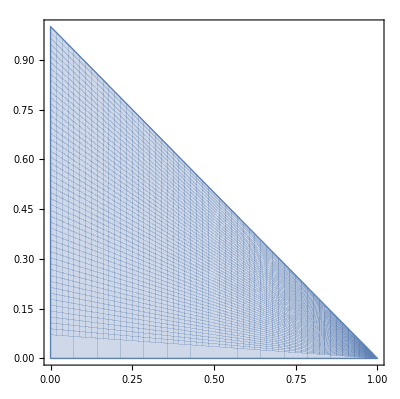

```mathematica
ParametricPlot[ {X,Y},{X,0,1},{Y,0,1-X}]
```

The  map from the reference element to a physical triangle 
	{p1,p2,p3}
we looked at before (anchored at p1) is
	P[{X, Y}] = p1 + X*(p2-p1)+Y*(p3-p1)
This lets us plot the triangle which means we have a simple way to describe where the triangle is! 
A fancy way of saying this is we have an easy parameterization of the triangle.

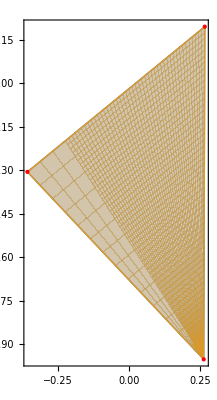

```mathematica
P[{p1_,p2_,p3_}][{X_,Y_}]:=p1 + X*(p2-p1)+Y*(p3-p1)
PA[{p1_,p2_,p3_}][{X_,Y_}]:=p1 + X*(p2-p1)+Y*(p3-p1)
PB[{p1_,p2_,p3_}][{X_,Y_}]:=p1 + X*(p2-p1)+Y*(p3-p1)
{p1,p2,p3}=RandomReal[{-1,1},{3,2}];
M= {p2-p1,p3-p1}ᵀ;
ParametricPlot[{
P[{p1,p2,p3}][{X,Y}],
p1 + M.{X,Y}
},{X,0,1},{Y,0,1-X},
Epilog->{Red, Point[{p1,p2,p3}]}]
```

It is easy to plot the three slab functions.  They are really just the images of the slab functions {1-X-Y,X,Y} on the reference triangle.

```mathematica
s1[{p1_,p2_,p3_}][{X_,Y_}]:=Join[p1 + X*(p2-p1)+Y*(p3-p1),{1-X-Y}]
s2[{p1_,p2_,p3_}][{X_,Y_}]:=Join[p1 + X*(p2-p1)+Y*(p3-p1),{X}]
s3[{p1_,p2_,p3_}][{X_,Y_}]:=Join[p1 + X*(p2-p1)+Y*(p3-p1),{Y}]
ParametricPlot3D[{
s1[{p1,p2,p3}][{X,Y}],
s2[{p1,p2,p3}][{X,Y}],
s3[{p1,p2,p3}][{X,Y}]
},{X,0,1},{Y,0,1-X}]
```

-Graphics3D-

This last approach is what is done in FENICS and GridAp and all the other FE codes.  It is much easier than any other way of doing things.  It makes all the triangles the same and means that all the computations are in a very real sense done in the reference element.  It works for fancier elements just the same way.

## Tent Functions

I am going to build a tent function at a chosen vertex of our mesh

```mathematica
Clear[ϕ]
ϕ[AllPoints_,TestTriangles_,{X_Symbol,Y_Symbol}][i_]:= Module[{AdjacentElements},
(* Grab elemnts including vertioex i *)
AdjacentElements = Select[ TestTriangles, MemberQ[#⟦1⟧,i]&]⟦All,1⟧;
(* Rotate the elements so that "i" is the first corner *)
 AdjacentElements = Map[RotateLeft[#,FirstPosition[#,i]⟦1⟧-1]&, AdjacentElements];
(* Build the approriate parametric slab functions *)
Table[
{p1,p2,p3}=AllPoints⟦AdjacentElements⟦j⟧⟧;
Join[p1 + X*(p2-p1)+Y*(p3-p1),{1-X-Y}],
{j, Length[AdjacentElements]}]
]
```

We should be able to tell if it is correct by plotting the things.

```mathematica
is={1, 2,15, 11};
Show[
Graphics3D[{ EdgeForm[Black],
Table[
{j1,j2,j3}=TestTriangles⟦i,1⟧;
{p1,p2,p3}=AllPoints⟦{j1,j2,j3}⟧;
{p1,p2,p3}=Map[Join[#,{0}]&,{p1,p2,p3}];
{Hue[i/m],Polygon[{p1,p2,p3}]},
{i,1,m}],
Table[
{x,y}=AllPoints⟦j⟧;
{Red,Line[{{x,y,0},{x,y,1}}],Text[j,{x,y,1},{-1,-1}]},
{j,1,Length[AllPoints]}]
}],
Table[
ParametricPlot3D[
Evaluate[ϕ[AllPoints,TestTriangles,{X,Y}][i]],
{X,0,1},{Y,0,1-X}],
{i,is}],
Axes->True,
Boxed->True
]
```

Table::iterb: Iterator {i,1,m} does not have appropriate bounds.

-Graphics3D-

## Interpolation Functions

We should be able to use all of  this to interpolate internal values. Right at the moment though it is a bit complicated because each tent is made up of of a a bunch of slab functions all defined on different triangles.

It would be easier to use piecewise linear functions which interpolated the three values on a single triangle.  Fortunately, this is pretty easy to do!

```mathematica
LinInterp[{{x1_,y1_},{x2_,y2_},{x3_,y3_}},{u1_,u2_,u3_}][{X_,Y_}]:={
x1+X*(x2-x1)+Y*(x3-x1),
y1+X*(y2-y1)+Y*(y3-y1),
u1*(1-X-Y)+u2*X+u3*Y}
{{x1,y1},{x2,y2},{x3,y3}}=RandomReal[{-5,5},{3,2}];
{u1,u2,u3}=RandomReal[{0,1},3];
Show[
ParametricPlot3D[ LinInterp[{{x1,y1},{x2,y2},{x3,y3}},{u1,u2,u3}][{X,Y}],
{X,0,1},
{Y,0,1-X}],
Graphics3D[{
{LightGreen,Polygon[{{x1,y1,0},{x2,y2,0},{x3,y3,0}}]},
{Red,PointSize[0.02], Point[{x1,y1,u1}],Point[{x2,y2,u2}],Point[{x3,y3,u3}]}
}],
PlotRange->All
]
```

-Graphics3D-

Now we can use this to interpolate a bunch of values on our mesh by combining all the triangles with the appropriate values.

```mathematica
f[{x_,y_}]:= √(36-(x^2+ y^2));
Allus=Map[f,AllPoints];
Hmm=Table[
js=TestTriangles⟦i,1⟧;
ps=AllPoints⟦js⟧;
us=Allus⟦js⟧;
ParametricPlot3D[ LinInterp[ps,us][{X,Y}],{X,0,1},{Y,0, 1-X},
PlotStyle->Hue[i/Length[TestTriangles]]
],
{i,Length[TestTriangles]}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
{Plot3D[f[{x,y}],{x,y}∈Omega],Show[Hmm,PlotRange->All]}
```

{-Graphics3D-,-Graphics3D-}

## Weak Form

Substituting u→∑_(i=1)^n a_i(t)ϕ_i(x) into or weak form 
	∫_Ω u_tt v dA +c∫_Ω u_t v dA =-k∫_Ω ∇u.∇vdA  
gives 
	∑_(i=1)^n a_i''∫_Ω ϕ_i(x)v dA +c ∑_(i=1)^n a_i'∫_Ω ϕ_i(x)v dA =-k∑_(i=1)^n a_i∫_Ω ∇ϕ_i.∇v(x) dA
Since this must hold for all v∈H_0^1((0,1)) it is actually an infinite number of equations!

An infinite number of equations is a problem!

From Linear Algebra we know we would like the same number of equations as unknowns!

Note: ϕ_j∈H_0^1(Ω) for j=1:n.

It is VERY convenient that there are n of them.

The simplest thing to do is to take the test functions v to match the trial functions u.

## Matrices

Choosing v=ϕ_j in our weak form gives
	∑_(i=1)^n a_i''∫_Ω ϕ_i(x)ϕ_i(x) dA +c ∑_(i=1)^n a_i'∫_Ω ϕ_i(x)ϕ_i(x) dA =-k∑_(i=1)^n a_i∫_Ω ∇ϕ_i.∇ϕ_i(x)dA

Since j=1:n there are n equations.

Linear equations including ODEs are naturally written using matrices

Define the mass matrix:  M_(j,i)=∫_Ω ϕ_i(x)ϕ_i(x) dA

Define the stiffness matrix:  K_(j,i)=k∫_Ω ∇ϕ_i.∇ϕ_i(x)dA

Our semi-discretized equation becomes
	∑_(i=1)^n a_i'' M_(j,i) +c ∑_(i=1)^n a_i' M_(j,i)  =-∑_(i=1)^n a_i K_(j,i)   
or 	∑_(i=1)^n M_(j,i)a_i'' +c ∑_(i=1)^n M_(j,i)a_i'  =-∑_(i=1)^n K_(j,i)a_i   
or 	M.a''[t]+c M.a'[t]=- K.a[t]

The matrices would be easy enough to compute VERY inefficiently!

```mathematica
KBuild[k_,n_]:= Table[
k*NIntegrate[∇ϕ[n,j][x]*∇ϕ[n,i][x],x∈Omega],
{j,n},{i,n}]
MBuild[n_]:= Table[
NIntegrate[ϕ[n,j][x]*ϕ[n,i][x],x∈Omega],
{j,n},{i,n}]
```

But instead we are going to work out how to build them efficiently!

We need to work out when triangles from different tent functions overlap and how to efficiently compute the required integral on the overlapping triangles.

We need to be able to integrate constants on triangles.

We need to be able to compute quadratics on triangles.

If we did fancier elements we might need fancier integrations.

```mathematica
n=12; k=0.1;
K=KBuild[k,n];
M=MBuild[n];
MatrixForm[K]
```

## Solving the ODEs.

The ODE system
	M.a''[t]+c M.a'[t]=- K.a[t]
is also easy to solve inefficiently!

```mathematica
n=12;
K=KBuild[0.1,n];
M=MBuild[n];
c=0.01; TMax=2.1;
a0=Table[ Sin[p[n,i]],{i,1,n}];
ad0=0*a0;
aSol = NDSolveValue[{
M.a''[t]+c M.a'[t]==-K.a[t],
a'[0]==ad0;
a[0]==a0},
a,{t,0, TMax}]
Plot[aSol[t],{t,0, TMax}]
```

```mathematica
MInvK=Inverse[M].K;
aSol = NDSolveValue[{
a''[t]+c a'[t]==-MInvK.a[t],
a'[0]==ad0,
a[0]==a0},
a,{t,0, TMax}]
Plot[aSol[t],{t,0, TMax}]
```

This is probably not the best way to look at the solution!